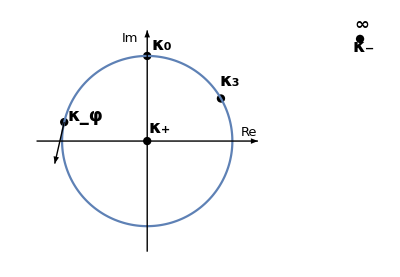

```mathematica
fi=-Pi/2+3Pi/7;
points=Graphics[{PointSize-> 0.015,Point[{0,0}],Point[{3^(1/2)/2,1/2}],Point[{0,1}],Point[{2.5,1.2}],Point[{-Cos[fi],-Sin[fi]}]}];
circ=ParametricPlot[{-Cos[t],-Sin[t]},{t,0,2 Pi},PlotRange->{{-1,1},{-1,1}}];
lines=Graphics[{Arrowheads->0.027,Arrow[{{0,-1.3},{0,1.3}}],Arrow[{{-1.3,0},{1.3,0}}],Arrow[{{-Cos[fi],-Sin[fi]},{-Cos[fi],-Sin[fi]}+{Sin[fi],-Cos[fi]}/2}]}];
texts=Graphics[{
Text[Style["κ_+",18,Bold],{0.15,0.15},FormatType->StandardForm],
Text[Style["Re",13],{1.2,0.1},FormatType->StandardForm],
Text[Style["Im",13],{-0.2,1.2},FormatType->StandardForm],
Text[Style["κ_0",18,Bold],{0.17,1.13},FormatType->StandardForm],
Text[Style["κ_φ",18,Bold],{-0.73,0.3},FormatType->StandardForm],
Text[Style["∞",18,Bold],{2.52,1.36},FormatType->StandardForm],
Text[Style["κ_-",18,Bold],{2.54,1.1},FormatType->StandardForm],
Text[Style["κ_3",18,Bold],{(3/4)^(1/2)+0.1,1/2+0.2},FormatType->StandardForm]
}];

Show[points,circ,lines,texts]
```

```mathematica
sph=Graphics3D[{Opacity[0.1],Specularity[White,10],Sphere[]},Boxed->False];
points3d=Graphics3D[{PointSize-> 0.015,Point[{0,0,-1}](*,Point[{3^(1/2)/2,1/2,0}]*),Point[{0,1,0}],Point[{0,0,1}],Point[{-Cos[fi],-Sin[fi],0}]}];
lines3d=Graphics3D[{Dashed,Thickness-> 0.001,Line[{{0,0,-1.5},{0,0,1.5}}],Line[{{0,1,0},{0,0,0}}],Line[{{-Cos[fi],-Sin[fi],0},0{Cos[fi],Sin[fi],0}}]}];
vectors3d=Graphics3D[{Arrowheads->0.027,Arrow[{{-Cos[fi],-Sin[fi],0},{-Cos[fi],-Sin[fi],0}+{Sin[fi],-Cos[fi],0}/2}]}];
texts3d=Graphics3D[{
Text[Style["κ_+",18,Bold],{0.15,0.19,1},FormatType->StandardForm],
Text[Style["κ_0",18,Bold],{0.17,1.13,0},FormatType->StandardForm],
Text[Style["κ_φ",18,Bold],{-0.73,0.3,0},FormatType->StandardForm],
Text[Style["κ_-",18,Bold],{0.15,0.2,-1},FormatType->StandardForm],
(*Text[Style["κ_3",18,Bold],{(3/4)^(1/2)+0.1,1/2+0.2},FormatType->StandardForm]*)
Text[Style["φ",14,Bold],{-0.15,0.2,0},FormatType->StandardForm]
}];
plo3d=ParametricPlot3D[{-Cos[t],-Sin[t],0},{t,0,2Pi}];
plo23d=ParametricPlot3D[0.4{-Cos[t],-Sin[t],0},{t,-Pi/2,fi},PlotStyle->{Dashed,Black}];
Show[sph,points3d,lines3d,plo3d,plo23d,vectors3d,texts3d,ImageSize->{400,300}]
```

-Graphics3D-